## Kapitola 7 - Kohonenova síť a Iris data

Demonstrace použití Kohonenovy neuronové sítě na datech z databáze UCI.

## Inicializace knihovny NeuralNetworks

Nejprve načteme knihovnu pro neuronové sítě.

```mathematica
<<NeuralNetworks`
```

Pokud pracujete v Mathematice 8.0, vypněte ještě zobrazování chybové hlášky Remove::rmnsm. Tuto hlášku vyhazují funkce knihovny NeuralNetworks. Na funkci knihovny toto nemá žádný vliv.

```mathematica
Off[Remove::rmnsm];
```

## Import dat

### Načtení dat ze souboru

Nastavíme si pracovní adresář na ten, kde máme uložen aktuální notebook, načítaná data musejí být ve stejném adresáři.

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
data=Import["iris.data"];
```

### Načtení dat přímo z internetu

Jiná možnost je importovat data přímo z internetu - příklad pro UCI databázi (stejná data jako v předchozím příkladu - načtení dat ze souboru).

```mathematica
data=Import["http://ftp.ics.uci.edu/pub/machine-learning-databases/iris/iris.data"];
```

## Předzpracování dat

Provedeme předzpracování dat pomocí stejného postupu, jaký je popsán v kapitole “Dopředná síť a Iris data”.

```mathematica
data2=Drop[data,-1];
inData=data2[[All,1;;4]];(*vstupní parametry*)
outDataTmp=data2[[All,5]];(*výstupní parametr*)
outVal=Tally[outDataTmp][[All,1]];
encode=MapIndexed[#1->Normal[SparseArray[#2->1,{Length[outVal]}]]&,outVal];
outData=Flatten[outDataTmp]/.encode;
```

## Zpracování dat neuronovou sítí

Nejdříve se podíváme na rozložení jednotlivých skupin vzorků v datech. Následující příkaz vykreslí vstupní data a jejich množství v jednotlivých skupinách.

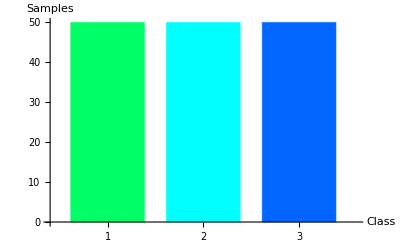

```mathematica
NetClassificationPlot[inData, outData, DataFormat -> BarChart, BarStyle -> {Hue[.4], Hue[.5], Hue[.6]}]
```

Vstupní data namapujeme sítí, jejíž uspořádání můžeme zadat. Čím víc neuronů použijeme, tím bude lépe pokryt prostor vstupních dat.

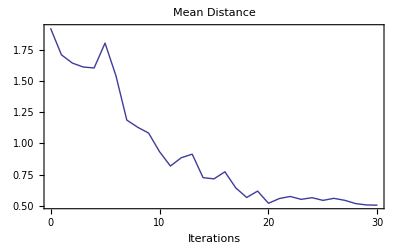

```mathematica
{somnet,fitrecord}=UnsupervisedNetFit[inData,6,SOM->{3,2}];
```

Vyhodnotíme síť pro nějaký vstupní vektor ze vstupních dat (můžeme použít i zcela nový). Vyjde nám souřednice vítězného vektoru (vektor s největší odezvou) v SOM struktuře.

```mathematica
somnet[{2.,0.6,0.4,2.2}]
```

{{1,2}}

Podívejme se na vyhodnocenou síť. Pole odpovídají jednotlivým neuronům. Neuron, který měl největší odezvu, se stal reprezentantem dané skupiny - první číslo, druhé číslo udává počet prvků, které k němu náleží.

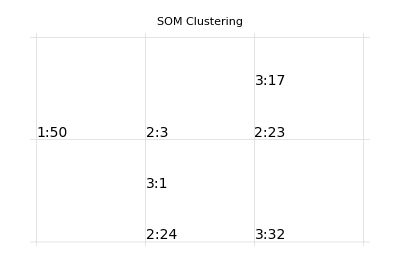

```mathematica
NetPlot[somnet,inData,outData]
```

Tímto příkazem si můžeme prohlédnout průběh učení.

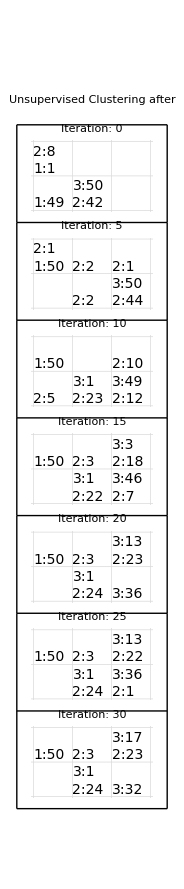

```mathematica
NetPlot[fitrecord,inData,outData]
```

Získaná síť může být použita na mapování jakýchkoliv vektorů (se správnou dimenzí, shodnou se vstupními vektory sítě). Výstup ukazuje ke kterému referenčnímu vektoru má nejblíže.

```mathematica
somnet[{{1,2,2,1},{0,0,0,0}}]
```

{{1,2},{1,2}}

Dále si můžeme nechat zobrazit hodnotu Eukleidovy vzdálenosti mezi jakýmkoliv vektorem a nejbližším referenčním vektorem. Ta nám udává, jak dobře odpovídá síť na předložená data.

```mathematica
UnsupervisedNetDistance[somnet,{{1,2,2,1},{0,0,0,0}}]
```

5.31752

Také lze smazat určité neurony z natrénované sítě pomocí příkazu NeuronDelete, kterému se zadávají souřadnice daných neuronů. Zde odstraňujeme 1. řádek a 2. slupec.

```mathematica
somnet2=NeuronDelete[somnet,{{1},{2}}]
```

UnsupervisedNet[{-Codebook Vectors-},{CreationDate → {2008, 6, 16, 16, 45, 40.40625}, Connect → False, SOM → {2, 1}, AccumulatedIterations → 30}]

Zobrazení sítě po smazání neuronů.

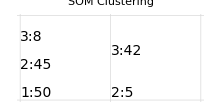

```mathematica
NetPlot[somnet2,inData,outData,DataFormat->Table]
```

Pokud je pokrytí už velmi dobré, můžeme nechat projít algoritmus učení opakovaně.  Při volbě Recursive -> False je délka kroku učícího algoritmu nastavena na jedničku pro všechny iterace, což se hodí právě pro situace, kdy jsou váhové vektory blízko svým optimálním hodnotám. Pro vektory vzdálené svému optimu může být tento způsob nestabilní.  Zatímco při Recursive -> True (výchozí hodnota) je délka kroku v prvních iteracích malá, takže váhové vektory najdou správnou orientaci. Poté je krok zvětšen, pro urychlení pokrytí. Od této vysoké hodnoty se délka kroku opět pomalu snižuje. Pokrytí je zaručeno, když se délka kroku blíží nule.
  Nejdříve se podíváme jak dopadne nenaučená síť s jednotlivými volbami.

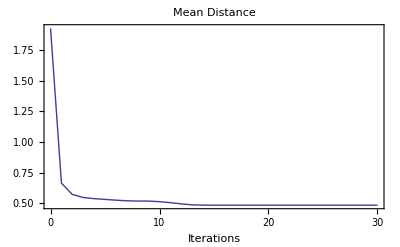

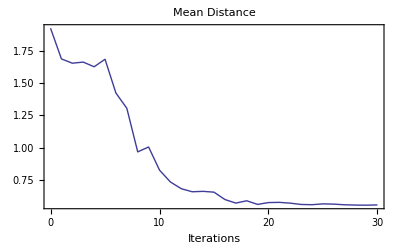

```mathematica
{fsomnet, fitrecord}=UnsupervisedNetFit[inData,6,SOM->{3,2},Recursive->False];
{tsomnet, fitrecord}=UnsupervisedNetFit[inData,6,SOM->{3,2},Recursive->True];
```

Doučení sítě, která byla vytvořena s parametrem Recursive -> False, nejprve opět s Recursive -> False, poté s hodnotou True.

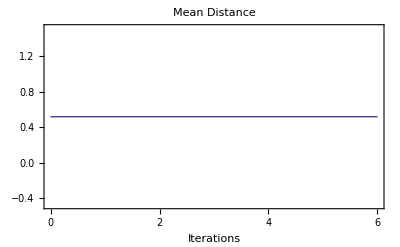

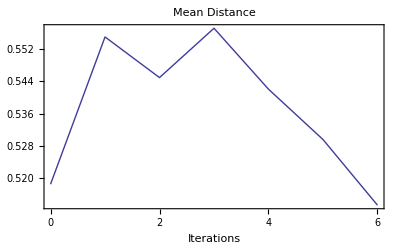

```mathematica
ffsomnet=UnsupervisedNetFit[inData,fsomnet,6,Recursive->False];
ftsomnet=UnsupervisedNetFit[inData,fsomnet,6,Recursive->True];
```

A doučení sítě, která byla vytvořena s parametrem Recursive -> True, nejprve  Recursive -> True, poté s hodnotou False.

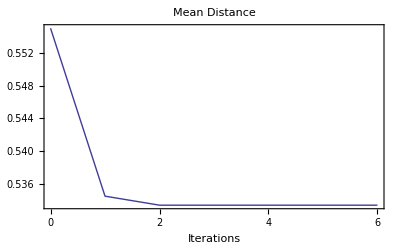

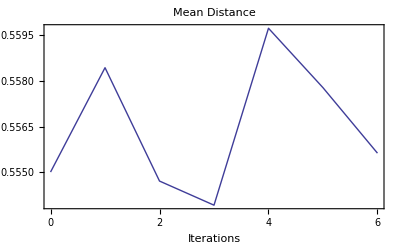

```mathematica
{tfsomnet,fitrecor}=UnsupervisedNetFit[inData,tsomnet,6,Recursive->False];
{ttsomnet,fitrecor}=UnsupervisedNetFit[inData,tsomnet,6,Recursive->True];
```

## Prohlášení

Tento text je součástí bakalářské práce Adama Činčury “Demonstrační aplikace pro podporu kurzu neuronových sítí” na FEL ČVUT 2011. Vznikl úpravou textu Petra Chlumského.